```mathematica
Quit[]
```

## Input

```mathematica
<<"/home/riccardo/Programs/FeynArts/FeynArts/FeynArts.m"
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

```mathematica
<<"/home/riccardo/Programs/FormCalc/FormCalc/FormCalc.m"
```

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

```mathematica
Remove[q1]
Remove[q2]
<<"/home/riccardo/Programs/ABISS/ABISS.m"
```

+++++ ABISS` +++++
Version 1.0.0

Amplitudes Builder, Interference Solver and Simplifier

A link to the model file SMbgf_Anglerfish.mod has been added to the FeynArts directory

A link to the model file SMbgf_FARAMIR_general_backup.mod has been added to the FeynArts directory

A link to the model file SMbgf_FARAMIR_general+SM.mod has been added to the FeynArts directory

A link to the model file SMbgfQCD_Anglerfish.mod has been added to the FeynArts directory

A link to the model file SMbgf_TelescopeOctopus_backup.mod has been added to the FeynArts directory

```mathematica
SetPath[NotebookDirectory[]];
```

Define the process:

```mathematica
SetProcess[{V[1]}->{S[1]}];
```

Generate default Input files

```mathematica
GenerateInput[];
```

Input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AH/input/kinematics.m already exist. It will NOT be overwritten.

Input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AH/input/integral_families.m already exist. It will NOT be overwritten.

Import the input files (kinematics + integral families).

```mathematica
ImportInput[];
```

Imported input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AH/input/integral_families.m.

Imported input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AH/input/kinematics.m.

## Diagrams generation

Generate diagrams using feynarts (charged current drell-yan, one loop boxes and born).

```mathematica
SetOptions[InsertFields,  Model -> "SMbgf_Anglerfish", GenericModel ->"Lorentzbgf", InsertionLevel->{Particles}, Restrictions->{NoQuarkMixing}, ExcludeParticles-> {}];
```

```mathematica
process={V[1]}->{S[1]};
```

```mathematica
topologies1L=CreateTopologies[1,1-> 1];
```

```mathematica
fields1L=InsertFields[topologies1L, process];
```

Excluding 24 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 15 Particles insertions

Restoring 24 field point(s)

in total: 15 Particles insertions

```mathematica
amp1L=CreateFeynAmp[fields1L];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 15 Particles amplitudes

in total: 15 Particles amplitudes

> Top. 1 ac/bd/cdcd.m, 0 diagrams

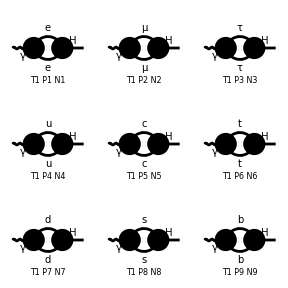

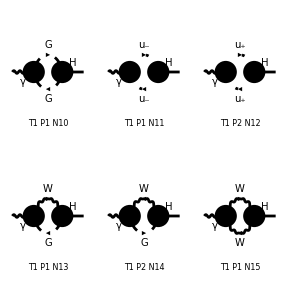

```mathematica
Paint[fields1L];
```

```mathematica
myAmp1L=ExtractAmplitude[amp1L];
```

```mathematica
SaveAmplitudes[myAmp1L,"OneLoopAmplitudes.m"];
```

Amplitudes saved in /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AH/feynArts_amplitudes/OneLoopAmplitudes.m

```mathematica
FullForm[myAmp1L[[5]]]
```

Times[Complex[0,Rational[-1,16]],Power[Pi,-4],FeynAmpDenominator[PropagatorDenominator[FourMomentum[Internal,1],MC],PropagatorDenominator[Plus[FourMomentum[Internal,1],Times[-1,FourMomentum[Outgoing,1]]],MC]],MatrixTrace[NonCommutative[Plus[MC,DiracSlash[Times[-1,FourMomentum[Internal,1]]]]],Plus[Times[Complex[0,1],EL,gHuu,MC,NonCommutative[ChiralityProjector[-1]]],Times[Complex[0,1],EL,gHuu,MC,NonCommutative[ChiralityProjector[1]]]],NonCommutative[Plus[MC,DiracSlash[Plus[Times[-1,FourMomentum[Internal,1]],FourMomentum[Outgoing,1]]]]],Plus[Times[Complex[0,1],EL,gAu,NonCommutative[DiracMatrix[Index[Lorentz,1]],ChiralityProjector[-1]]],Times[Complex[0,1],EL,gAu,NonCommutative[DiracMatrix[Index[Lorentz,1]],ChiralityProjector[1]]]]],PolarizationVector[V[1],FourMomentum[Incoming,1],Index[Lorentz,1]],SumOver[Index[Colour,3],3]]

## Projection and polarization vector

```mathematica
p[Lor1_]:=- I SP[p1,{Lor1}]/SP[p1,p1]
```

### Remove polarization vectors

```mathematica
removePolarizationVectors={PolarizationVector[V[1],p_,i_]->1}
```

{ep[V[1],p_,i_]→1}

## Interference

```mathematica
myAmp1LABISS=Map[AmpSquare[#,1]&,myAmp1L];
```

```mathematica
myAmp1LnoEP=myAmp1LABISS/.removePolarizationVectors;
```

```mathematica
myAmp1LProjection=Map[AmpSquare[#*p[Lor1],1]&,myAmp1LnoEP];
```

```mathematica
myAmp1LnoEP[[1]]
```

1/(4 π^4)ⅈ EL^2 gAl gHll ME^2 KiraPropagator[q1,ME] KiraPropagator[-p1+q1,ME] (SP[p1,{Lor1}]-2 SP[q1,{Lor1}])

```mathematica
myAmp1LProjection[[1]]
```

(EL^2 gAl gHll ME^2 KiraPropagator[q1,ME] KiraPropagator[-p1+q1,ME] (psq-2 SP[p1,q1]))/(4 π^4 psq)

```mathematica
SquareSimplifyAndSave[myAmp1LProjection,{1}]
```

Computed contribution 1-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AH//interferences/Contribution_1_1.m.

Computed contribution 2-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AH//interferences/Contribution_2_1.m.

Computed contribution 3-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AH//interferences/Contribution_3_1.m.

Computed contribution 4-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AH//interferences/Contribution_4_1.m.

Computed contribution 5-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AH//interferences/Contribution_5_1.m.

Computed contribution 6-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AH//interferences/Contribution_6_1.m.

Computed contribution 7-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AH//interferences/Contribution_7_1.m.

Computed contribution 8-1.

Computed contribution 9-1.

Computed contribution 10-1.

Computed contribution 11-1.

Computed contribution 12-1.

Computed contribution 13-1.

Computed contribution 14-1.

Computed contribution 15-1.

## Shift

```mathematica
ImportInput[];
```

Imported input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AH/input/integral_families.m.

Imported input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AH/input/kinematics.m.

```mathematica
Do[
ShiftAndSave[i,j,False];
,{i,15},{j,1}]
```

Integral family {{A0, {ME}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AH/interferences/Contribution_1_1.m.

Integral family {{A0, {MM}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AH/interferences/Contribution_2_1.m.

Integral family {{A0, {ML}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AH/interferences/Contribution_3_1.m.

Integral family {{A0, {MU}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AH/interferences/Contribution_4_1.m.

Integral family {{A0, {MC}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AH/interferences/Contribution_5_1.m.

Integral family {{A0, {MT}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AH/interferences/Contribution_6_1.m.

Integral family {{A0, {MD}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AH/interferences/Contribution_7_1.m.

Integral family {{A0, {MS}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AH/interferences/Contribution_8_1.m.

Integral family {{A0, {MB}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AH/interferences/Contribution_9_1.m.

Integral family {{A0, {MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AH/interferences/Contribution_10_1.m.

Integral family {{A0, {MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AH/interferences/Contribution_11_1.m.

Integral family {{A0, {MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AH/interferences/Contribution_12_1.m.

Integral family {{A0, {MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AH/interferences/Contribution_13_1.m.

Integral family {{A0, {MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AH/interferences/Contribution_14_1.m.

Integral family {{A0, {MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AH/interferences/Contribution_15_1.m.

## KiraInput

```mathematica
Do[
GenerateAndSaveKiraInput[i,j];
,{i,15},{j,1}]
```

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AH/kira_input/Contribution_1_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AH/kira_input/Contribution_2_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AH/kira_input/Contribution_3_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AH/kira_input/Contribution_4_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AH/kira_input/Contribution_5_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AH/kira_input/Contribution_6_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AH/kira_input/Contribution_7_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AH/kira_input/Contribution_8_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AH/kira_input/Contribution_9_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AH/kira_input/Contribution_10_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AH/kira_input/Contribution_11_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AH/kira_input/Contribution_12_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AH/kira_input/Contribution_13_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AH/kira_input/Contribution_14_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AH/kira_input/Contribution_15_1.m.

```mathematica
PrintScalarIntegrals[]
```

{userIntegral[A0,{ME},1,1],userIntegral[A0,{ME},0,1],userIntegral[A0,{ME},1,0],userIntegral[A0,{MM},1,1],userIntegral[A0,{MM},0,1],userIntegral[A0,{MM},1,0],userIntegral[A0,{ML},1,1],userIntegral[A0,{ML},0,1],userIntegral[A0,{ML},1,0],userIntegral[A0,{MU},1,1],userIntegral[A0,{MU},0,1],userIntegral[A0,{MU},1,0],userIntegral[A0,{MC},1,1],userIntegral[A0,{MC},0,1],userIntegral[A0,{MC},1,0],userIntegral[A0,{MT},1,1],userIntegral[A0,{MT},0,1],userIntegral[A0,{MT},1,0],userIntegral[A0,{MD},1,1],userIntegral[A0,{MD},0,1],userIntegral[A0,{MD},1,0],userIntegral[A0,{MS},1,1],userIntegral[A0,{MS},0,1],userIntegral[A0,{MS},1,0],userIntegral[A0,{MB},1,1],userIntegral[A0,{MB},0,1],userIntegral[A0,{MB},1,0],userIntegral[A0,{MW},1,1],userIntegral[A0,{MW},0,1],userIntegral[A0,{MW},1,0]}

```mathematica
SaveScalarIntegrals["scalar_integrals"];
```

```mathematica
ExportScalarIntegrals["kira_scalar_integrals.dat"];
```

## Apply Kira sub;

```mathematica
ImportScalarIntegrals["scalar_integrals"];
```

```mathematica
ClearRules[]
```

{}

```mathematica
ImportRules[NotebookDirectory[]<>"kira_myintegrals.m"]
```

```mathematica
PrintRules[]
```

{userIntegral[A0,{m1},0,1]→userIntegral[A0,{m1},1,0]}

```mathematica
PrintScalarIntegrals[]
```

{userIntegral[A0,{ME},1,1],userIntegral[A0,{ME},0,1],userIntegral[A0,{ME},1,0],userIntegral[A0,{MM},1,1],userIntegral[A0,{MM},0,1],userIntegral[A0,{MM},1,0],userIntegral[A0,{ML},1,1],userIntegral[A0,{ML},0,1],userIntegral[A0,{ML},1,0],userIntegral[A0,{MU},1,1],userIntegral[A0,{MU},0,1],userIntegral[A0,{MU},1,0],userIntegral[A0,{MC},1,1],userIntegral[A0,{MC},0,1],userIntegral[A0,{MC},1,0],userIntegral[A0,{MT},1,1],userIntegral[A0,{MT},0,1],userIntegral[A0,{MT},1,0],userIntegral[A0,{MD},1,1],userIntegral[A0,{MD},0,1],userIntegral[A0,{MD},1,0],userIntegral[A0,{MS},1,1],userIntegral[A0,{MS},0,1],userIntegral[A0,{MS},1,0],userIntegral[A0,{MB},1,1],userIntegral[A0,{MB},0,1],userIntegral[A0,{MB},1,0],userIntegral[A0,{MW},1,1],userIntegral[A0,{MW},0,1],userIntegral[A0,{MW},1,0]}

```mathematica
DetermineMasterIntegrals[]
```

```mathematica
PrintMasterIntegrals[]
```

{userIntegral[A0,{ME},1,1],userIntegral[A0,{ME},1,0],userIntegral[A0,{MM},1,1],userIntegral[A0,{MM},1,0],userIntegral[A0,{ML},1,1],userIntegral[A0,{ML},1,0],userIntegral[A0,{MU},1,1],userIntegral[A0,{MU},1,0],userIntegral[A0,{MC},1,1],userIntegral[A0,{MC},1,0],userIntegral[A0,{MT},1,1],userIntegral[A0,{MT},1,0],userIntegral[A0,{MD},1,1],userIntegral[A0,{MD},1,0],userIntegral[A0,{MS},1,1],userIntegral[A0,{MS},1,0],userIntegral[A0,{MB},1,1],userIntegral[A0,{MB},1,0],userIntegral[A0,{MW},1,1],userIntegral[A0,{MW},1,0]}

```mathematica
Do[
SaveResult[i,j];
,{i,15},{j,1}]
```

## Ward Identity Test

### Total coefficients

```mathematica
diagramCoefficients= {};
Do[diagramCoefficients=Append[diagramCoefficients,<<(NotebookDirectory[]<>"coefficients/Coefficients_"<>ToString[i]<>"_1.m")],{i,15}]
```

```mathematica
diagramCoefficients
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(EL^2 ggmgmA gHgmgm)/(64 π^4),0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(EL^2 ggpgpA gHgpgp)/(64 π^4),0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(3 EL^2 gFAW gHFW)/(32 π^4),0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(3 EL^2 gFAW gHFW)/(32 π^4),0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
coefficients=Plus@@diagramCoefficients
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(EL^2 ggmgmA gHgmgm)/(64 π^4)-(EL^2 ggpgpA gHgpgp)/(64 π^4),0}

### Lagrangian parameter replace

```mathematica
<<(NotebookDirectory[]<>"smparameters.m")
parameterReplace=smparameters
```

{gZlL→(-1/2+SW^2)/(CW SW),gZlR→SW/CW,gZNL→1/(2 CW SW),gZuL→(1/2-(2 SW^2)/3)/(CW SW),gZuR→-(2 SW)/(3 CW),gZdL→(-1/2+SW^2/3)/(CW SW),gZdR→SW/(3 CW),gAl→1,gAu→-2/3,gAd→1/3,gWNl→1/(√2 SW),gWlN→1/(√2 SW),gWud→1/(√2 SW),gWdu→1/(√2 SW),gWWZ→CW/SW,gWWA→1,gWWWW→1/SW^2,gWWZZ→-CW^2/SW^2,gWWAZ→CW/SW,gWWAA→-1,gHHHH→-3/(4 MW^2 SW^2),gXXXX→-3/(4 MW^2 SW^2),gHHXX→1/(2 SW^2),gHHFF→1/(2 SW^2),gXXFF→1/(2 SW^2),gFFFF→1/(2 SW^2),gHXFF→1/(4 CW^2),gHHH→-3/(2 MW SW),gHXX→-1/(2 MW SW),gHFF→-1/(2 MW SW),gXFF→(MW SW)/(2 CW^2),gHHZZ→1/(2 CW^2 SW^2),gXXZZ→1/(2 CW^2 SW^2),gHHWW→1/(2 SW^2),gXXWW→1/(2 SW^2),gFFWW→1/(2 SW^2),gFFAA→2,gFFAZ→(-CW^2+SW^2)/(CW SW),gFFZZ→((-CW^2+SW^2)^2)/(2 CW^2 SW^2),gHFAW→-1/(2 SW),gHFZW→-1/(2 CW),gXFAW→1/(2 SW),gHFZW→-1/(2 CW),gXFZW→1/(2 CW),gHXWW→1/(2 SW^2),gHXZ→1/(2 CW SW),gFFA→1,gFFZ→(CW^2-SW^2)/(2 CW SW),gHFW→1/(2 SW),gXFW→1/(2 SW),gHZZ→MW/(CW^2 SW),gHWW→MW/SW,gXWW→MW/SW,gFAW→-MW,gFZW→MW/CW,gHll→-1/(2 MW SW),gHuu→-1/(2 MW SW),gHdd→-1/(2 MW SW),gXll→1/(2 MW SW),gXuu→1/(2 MW SW),gXdd→1/(2 MW SW),gFll→1/(√2 MW SW),gFud→1/(√2 MW SW),gFdu→1/(√2 MW SW),ggpgpA→1,ggmgmA→1,ggpgpZ→CW/SW,ggmgmZ→CW/SW,ggzgpW→CW/SW,ggzgmW→CW/SW,ggagpW→1,ggagmW→1,gHgzgz→-MW/(CW^2 SW),gHgpgp→-MW/SW,gHgmgm→-MW/SW,gXgpgp→MW/(2 SW),gXgmgm→MW/(2 SW),gFgzgp→MW/CW,gFgzgm→MW/CW,gFgagm→MW,gFgagp→MW,ggpgpAA→1,ggmgmAA→1,ggpgpAZ→-CW/SW,ggmgmAZ→-CW/SW,ggpgpZZ→CW^2/SW^2,ggmgmZZ→CW^2/SW^2,ggagpAW→-1,ggagmAW→-1,ggagpZW→CW/SW,ggagmZW→CW/SW,ggzgpAW→CW/SW,ggzgmAW→CW/SW,ggzgpZW→-CW^2/SW^2,ggzgmZW→-CW^2/SW^2,ggagaWW→1,ggagzWW→-CW/SW,ggzgzWW→CW^2/SW^2,ggpgpWW→1/SW^2,ggmgmWW→1/SW^2,ggpgmWW→-1/SW^2,gHHgzgz→-1/(2 CW^2 SW^2),gHHgpgp→-1/(2 SW^2),gHHgmgm→-1/(2 SW^2),gXXgzgz→-1/(2 CW^2 SW^2),gXXgpgp→-1/(2 SW^2),gXXgmgm→-1/(2 SW^2),gFFgaga→-1,gFFgzgz→((CW^2-SW^2)^2)/(2 CW^2 SW^2),gFFgpgp→-1/(2 SW^2),gFFgmgm→-1/(2 SW^2),gFFgagz→(CW^2-SW^2)/(CW SW),gHXgpgp→1/(4 SW^2),gHXgmgm→1/(4 SW^2),gHFgagp→1/(2 SW),gHFgagm→1/(2 SW),gHFgzgp→1/(2 CW),gHFgzgm→1/(2 CW),gXFgagp→1/(2 SW),gXFgagm→1/(2 SW),gXFgzgp→1/(2 CW),gXFgzgm→1/(2 CW)}

```mathematica
coefficients/.parameterReplace//Simplify
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}